## input integrand

```mathematica
Block[{phi=100,gphi=100,dphi=100,as=1,at=1,M=1,m=1},
Clear[V,M4,x,r,H];
V=((gphi/as)^2+(m phi)^2)/2;
M4=M^4;
x:=p^2/M^4;
r:=√(1+2x(1+V/M4))-1;
H:=M4 (r+Log[r/x]);

Print["Cos[as^3dphi p]Exp[-as^3at H] = ",Cos[as^3 dphi p]Exp[-as^3 at H]];

answer1:=∫_0^∞ Cos[as^3 dphi p]Exp[-as^3 at H]ⅆp;
Print["answer1 = ",Timing[answer1]];
]
```

Cos[as^3dphi p]Exp[-as^3at H] = (ⅇ^(1-√(1+20002 p^2)) p^2 Cos[100 p])/(-1+√(1+20002 p^2))

answer1 = {4.35505,∫_0^∞ (ⅇ^(1-√(1+20002 p^2)) p^2 Cos[100 p])/(-1+√(1+20002 p^2))ⅆp}

## explore integrand

### integrand

```mathematica
Clear[f];
f[p_]:=(ⅇ^(1-√(1+20002 p^2)) p^2 Cos[100 p])/(-1+√(1+20002 p^2));
```

### damping

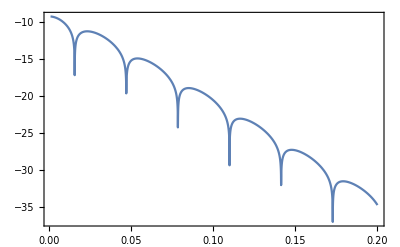

```mathematica
Plot[Log[Abs[f[p]]],{p,0.001,0.2},Frame->True]
```

#### oscillatory term

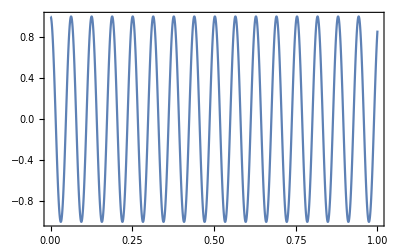

```mathematica
Plot[ Cos[100 p],{p,0,1},Frame->True]
```

### table of function values

```mathematica
Table[
{10^k,f[10^k]}//N
,{k,-3,10}]//TableForm
```

0.001 | 0.0000989954
0.01 | 0.0000354904
0.1 | -1.20433×10^-9
1. | 6.30051×10^-64
10. | 6.5778747853977×10^-616
100. | -1.27037615837728×10^-6142
1000. | -4.98879340246746×10^-61421
10000. | 2.51490515523938×10^-614214
100000. | -4.93042676066182×10^-6142156
1.×10^6 | -2.28047221332422×10^-61421582
1.×10^7 | 2.21790184597686×10^-614215850
1.×10^8 | 4.1192844241139433924881982400006137695`15.954589770191005*^-6142158543
1.×10^9 | 5.66053825561376259086882481308930143`15.954589770191005*^-61421585480
1.×10^10 | 1.5178254852099844094490324865432201021976095`15.954589770191005*^-614215854853

### composite function

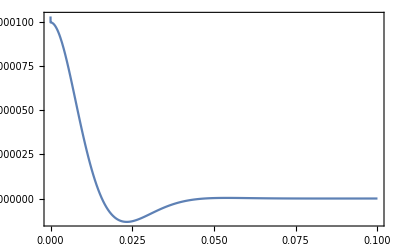

```mathematica
Plot[f[p],{p,0,0.1},PlotRange->Full,PlotPoints->200,Frame->True]
```

## integration over finite domains

```mathematica
Limit[f[p],p->0]
```

1/10001

```mathematica
Clear[g]
g[p_]:=1/10001 /; p==0;
g[p_]:=f[p] /; p>0;
```

```mathematica
Table[
answer=NIntegrate[g[p],{p,0,10^ω},PrecisionGoal->6];
Print[answer,": integrating from 0 to ",10^ω];
,{ω,3}];
```

6.3475×10^-7: integrating from 0 to 10

6.3475×10^-7: integrating from 0 to 100

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.137761}. NIntegrate obtained 6.3475×10^-7 and 4.49642×10^-12 for the integral and error estimates.

6.3475×10^-7: integrating from 0 to 1000

### tinker

```mathematica
Series[-1+√(1+α x^2),{x,∞,4}]
```

√α x-1+1/(2 √α x)-1/(8 α^(3/2) x^3)+O[1/x]^5

```mathematica
Series[-1+√(1+α x^2),{x,0,4}]
```

(α x^2)/2-(α^2 x^4)/8+O[x]^5

```mathematica
Series[-1+√(1+α x^2),{x,1,4}]
```

(-1+√(1+α))+(α (x-1))/(√(1+α))+(α (x-1)^2)/(2 (1+α)^(3/2))-(α^2 (x-1)^3)/(2 (1+α)^(5/2))+((-α^2+4 α^3) (x-1)^4)/(8 (1+α)^(7/2))+O[x-1]^5